# Solving Differential Equations

## The Basics

A differential equation is an equality in which the terms involve one or more unknown functions and their derivatives. In general, a solution to a differential equation is a function (or a class of functions) that make the differential equation true.

The simples way to solve a differential equation in Mathematica is by using the DSolve function.

```mathematica
DSolve[eqn,u,x]
```

```mathematica
DSolve[{Subscript[eqn, 1],Subscript[eqn, 2],…},{Subscript[u, 1],Subscript[u, 2],…},…]
```

```mathematica
DSolve[eqn,u,{Subscript[x, 1],Subscript[x, 2],…}]
```

The syntax is such that on the first argument one places the equation, on the second argument one places the unknown function, and on the third argument the independent variables. A few examples follow:

```mathematica
DSolve[y[x]==y'[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]}}

```mathematica
DSolve[y[x]==y'[x],y,x]
```

{{y→Function[{x},ⅇ^x C[1]]}}

You can check the solution satisfies the equation

```mathematica
y[x]==y'[x]/.%
```

{True}

Notice how depending on whether we write the function with arguments on the second argument, or ask for the pure function itself (just the name with no arguments) we get slightly different results. The first corresponds to y[x] being equal to to an expression in terms of x, while the second one to an abstract function that can admit input parameters and return a value

For example we can feed it Log[3] to obtain 3 c_1

```mathematica
Function[{x},ⅇ^x C[1]][Log[3]]
```

3 C[1]

Notice how the results are given as a list of lists this is to make up for the fact that there could be more than one family of solutions

```mathematica
DSolve[y'[x]^2== x^2,y[x],x]
```

{{y[x]→-x^2/2+C[1]},{y[x]→x^2/2+C[1]}}

In the case where there is only one solution and you want to extract it directly, perhaps to perform a specific computation you may

```mathematica
DSolveValue[y'[x]== x,y[x],x]
```

x^2/2+C[1]

```mathematica
DSolveValue[y'[x]== x,y,x]
```

Function[{x},x^2/2+C[1]]

```mathematica
DSolveValue[y'[x]^2== x^2,y[x],x]
```

DSolveValue::dsvb: There are multiple solution branches for the equations, but DSolveValue will return only one. Use DSolve to get all of the solution branches.

-x^2/2+C[1]

There are several ways in which one can use these results for further computation. For example

```mathematica
gExp=DSolveValue[y'[x]==y[x],y,x]
```

Function[{x},ⅇ^x C[1]]

```mathematica
gExp[Log[3]]
```

3 C[1]

```mathematica
fExp[a_]:=(DSolve[y'[x]==y[x],y[x],x][[1,1,2]])/.x->a
```

```mathematica
fExp[Log[3]]
```

3 C[1]

We can add initial conditions say y[0]=1 by letting the first parameter be a list with the equation and the additional conditions. And thus we would get more precise solutions.

```mathematica
DSolve[{y'[x]==y[x],y[0]==2},y[x],x]
```

{{y[x]→2 ⅇ^x}}

And thus we can plot solutions to differential equations in several ways one of which is illustrated below.

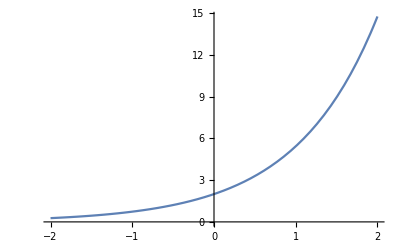

```mathematica
Plot[DSolveValue[{y'[x]==y[x],y[0]==2},y,x][a],{a,-2,2}]
```

We can get simultaneous solutions by making a list of functions on the second parameter

```mathematica
DSolve[{y'[x]==z[x],z'[x]==-y[x],y[0]==0,z[0]==1},{y[x],z[x]},x]
```

{{y[x]→Sin[x],z[x]→Cos[x]}}

```mathematica
DSolve[{x'[s]==Cos[t[s]],y'[s]==Sin[t[s]],t'[s]==s,x[0]==0,y[0]==0,t[0]==0},{x[s],y[s],t[s]},s]
```

{{t[s]→s^2/2,x[s]→√π FresnelC[s/(√π)],y[s]→√π FresnelS[s/(√π)]}}

A first order PDE

```mathematica
eqn=x^2*D[u[x,y],x]+y^2*D[u[x,y],y]-(x+y)*u[x,y];
sol=DSolve[eqn==0,u,{x,y}]
```

{{u→Function[{x,y},x y C[1][1/x-1/y]]}}

```mathematica
fn=u[x,y]/.%⟦1⟧/.{ C[1][t_]->Sin[t^2]+t/10}
```

x y (1/10 (1/x-1/y)+Sin[(1/x-1/y)^2])

```mathematica
Plot3D[%,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

You can solve Differential Algebraic Equations

```mathematica
{f''[x]==g[x],f[x]+g[x]==3 Sin[x],f[Pi]==1,f'[Pi]==0};
DSolve[%,{f,g},x]
```

{{f→Function[{x},1/2 (-2 Cos[x]+3 π Cos[x]-3 x Cos[x]+3 Sin[x])],g→Function[{x},1/2 (2 Cos[x]-3 π Cos[x]+3 x Cos[x]+3 Sin[x])]}}

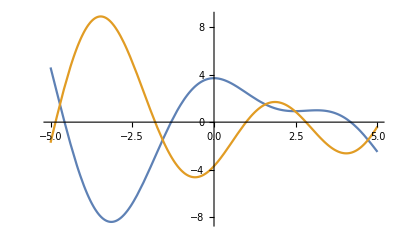

```mathematica
Plot[{f[x]/.%,g[x]/.%},{x,-5,5}]
```

## Classification of DiffEqs

Order

Linearity

Degree

```mathematica
Manipulate[Plot3D[EllipticF[x,t],{x,-10,-n},{t,-10,-n},PlotRange->All,PerformanceGoal->"Quality"],{n,5,-10}]
```

```mathematica
Manipulate[Plot3D[JacobiAmplitude[u,m],{u,-n,n},{m,-n,n},PerformanceGoal->"Quality"],{n,1,10}]
```

## ODEs

Exact Solutions

Numerical Solutions

Qualitative Theory

Uniqueness and Existence theorems

```mathematica
SystemOpen["https://reference.wolfram.com/language/tutorial/DSolveOrdinaryDifferentialEquations.html"]
```

```mathematica
{{"separable",y'[x]==f[x]g[y],1691,"G. Leibniz"},
{"homogeneous",y'[x]== f[x/y[x]],1691,"G. Leibniz"},
{"linear first-order ODE",y'[x]+P[x]y[x]==Q[x],1694,"G.Leibniz"},
{,,,},
{"Bernoulli",y'[x]+P[x]y[x]== Q[x] y[x]^n,1695, "James Bernoulli"},
{"Riccati", y'[x]==f[x]+g[x]y[x]+h[x] y[x]^2,1724,"Count Riccati"},
{"exact first-order ODE", Row[{HoldForm[M ⅆx + Nⅆy==0]," with ",HoldForm[D[M, y]==D[N, x]]}],1734,"L. Euler"} ,
{,,,},
{"Clairaut", y[x]==x y'[x]+f[y'[x]],1734, "A-C. Clairaut"},
{"Linear with constant coefficients",Row[{"y^(n)(x) + a_(n - 1)y^(n-1)(x)+ ... +a_0 y(x) = P(x)"//TraditionalForm," with ",Subscript[a, i]," constant"}],1743,"L. Euler"},
{"hypergeometric",TraditionalForm[x(1-x)y''[x]+(c-(a+b+1)x)y'[x]-a b y[x]==0],1769, "L Euler"},
{,,,},
{"Legendre",(1-x^2)y''[x]-2x  y'[x] + n(n+1)y[x]==0,1785,"M. Legendre"},
{"Bessel",x^2 y''[x]+x yu'[x]+(x^2-n^2)y[x]==0,1824,"F. Bessel"},
{"Mathieu",y''[x]+(a-2q Cos[2x])y[x]==0,1868,"E. Mathieu"},
{,,,},
{"Abel",y'[x]==f[x]+g[x]y[x]+h[x] y[x]^2+k[x] y[x]^3,1834,"N. H. Abel"},
{"Chini",y'[x]==f[x]+g[x]y[x]+h[x] y[x]^n,1924,"M. Chini"}
}//(Grid/*TraditionalForm)
```

separable | y'(x)==f(x) g(y) | 1691 | G. Leibniz
homogeneous | y'(x)==f(x/(y(x))) | 1691 | G. Leibniz
linear first-order ODE | P(x) y(x)+y'(x)==Q(x) | 1694 | G.Leibniz
 |  |  | 
Bernoulli | P(x) y(x)+y'(x)==Q(x) (y(x))^n | 1695 | James Bernoulli
Riccati | y'(x)==f(x)+g(x) y(x)+h(x) (y(x))^2 | 1724 | Count Riccati
exact first-order ODE | M ⅆx+N ⅆy==0 with (∂M)/(∂y)==(∂N)/(∂x) | 1734 | L. Euler
 |  |  | 
Clairaut | y(x)==f(y'(x))+x y'(x) | 1734 | A-C. Clairaut
Linear with constant coefficients | y^(n)(x) + a_(n - 1)y^(n-1)(x)+ ... +a_0 y(x) = P(x) with a_i constant | 1743 | L. Euler
hypergeometric | y'(x) (c-x (a+b+1))-a b y(x)+(1-x) x y''(x)==0 | 1769 | L Euler
 |  |  | 
Legendre | n (n+1) y(x)+(1-x^2) y''(x)-2 x y'(x)==0 | 1785 | M. Legendre
Bessel | (x^2-n^2) y(x)+x^2 y''(x)+x yu'(x)==0 | 1824 | F. Bessel
Mathieu | y(x) (a-2 q cos(2 x))+y''(x)==0 | 1868 | E. Mathieu
 |  |  | 
Abel | y'(x)==f(x)+g(x) y(x)+h(x) (y(x))^2+k(x) (y(x))^3 | 1834 | N. H. Abel
Chini | y'(x)==f(x)+g(x) y(x)+h(x) (y(x))^n | 1924 | M. Chini

#### Straight Integration

Sometimes the differential equation can be solved by just integrating, but DSolve still does the trick

```mathematica
DSolve[y'[x]==x^2 Sin[x]+Sqrt[1+x^2],y[x],x]
```

{{y[x]→1/2 x √(1+x^2)+ArcSinh[x]/2+C[1]-(-2+x^2) Cos[x]+2 x Sin[x]}}

```mathematica
Integrate[x^2 Sin[x]+Sqrt[1+x^2],x]
```

1/2 x √(1+x^2)+ArcSinh[x]/2-(-2+x^2) Cos[x]+2 x Sin[x]

Notice how the main difference is the constant of integration. We can obtain the general antiderivative using the GeneratedParameters option using the

```mathematica
Integrate[x^2 Sin[x]+Sqrt[1+x^2],x,GeneratedParameters->C]
```

1/2 x √(1+x^2)+ArcSinh[x]/2+C[1]-(-2+x^2) Cos[x]+2 x Sin[x]

#### Separable Equations

```mathematica
DSolve[y'[x]==x^2 y[x]^2/(√(3-x^2)),y[x],x]
```

{{y[x]→2/(x √(3-x^2)-3 ArcSin[x/(√3)]-2 C[1])}}

```mathematica
Solve[Integrate[1/y[x]^2,y[x]]==Integrate[x^2/(√(3-x^2)),x],y[x]]
```

{{y[x]→2/(x √(3-x^2)-3 ArcSin[x/(√3)])}}

```mathematica
Solve[Integrate[1/y[x]^2,y[x]]==Integrate[x^2/(√(3-x^2)),x,GeneratedParameters->C],y[x]]
```

{{y[x]→2/(x √(3-x^2)-3 ArcSin[x/(√3)]-2 C[1])}}

```mathematica
DSolve[y'[x]==(x^2 Exp[y[x]])/Sqrt[3-x^2],y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},-Log[1/2 x √(3-x^2)-3/2 ArcSin[x/(√3)]-C[1]]]}}

```mathematica
DSolve[y'[x]==(x^2)/(Sqrt[9-x^2] Log[y[x]]*Sin[y[x]]),y[x],x]
```

{{y[x]→InverseFunction[CosIntegral[#1]-Cos[#1] Log[#1]&][-1/2 x √(9-x^2)+9/2 ArcSin[x/3]+C[1]]}}

#### Homogeneous equations

Recall that homogeneous equations are those in which the total degree of both the numerator and the denominator are the same

```mathematica
sol=DSolve[y'[x]==(-(x^2-3 y[x]^2))/(x y[x]),y,x]
```

{{y→Function[{x},-(√(x^2+2 x^6 C[1]))/(√2)]},{y→Function[{x},(√(x^2+2 x^6 C[1]))/(√2)]}}

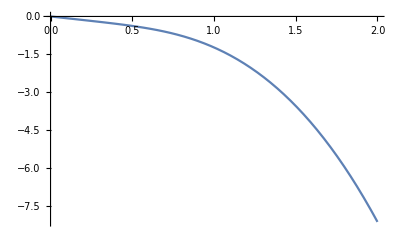

```mathematica
Plot[y[x]/.sol[[1]]/.C[1]->1,{x,0,2}]
```

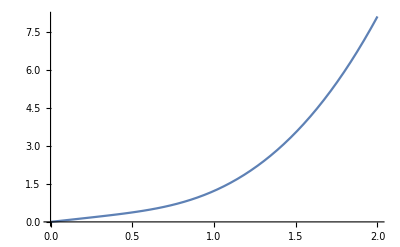

```mathematica
Plot[y[x]/.sol[[2]]/.C[1]->1,{x,0,2}]
```

This gives us an idea on how the two families behave

```mathematica
DSolve[{y'[x]==(-(x^2-3 y[x]^2))/(x y[x]),y[1]==3},y[x],x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{{y[x]→(√(x^2 (1+17 x^4)))/(√2)}}

Note how the family for the negative solution cannot possibly satisfy the boundary condition, that is why the message is displayed.

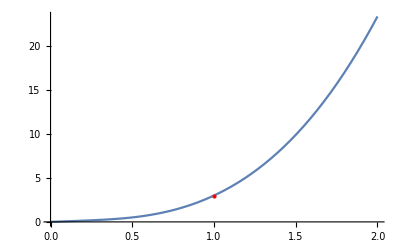

```mathematica
Plot[%[[1,1,2]],{x,0,2},Epilog->{Red ,PointSize[Large],Point[{1,3}]}]
```

#### Linear first-order equations

```mathematica
DSolve[y'[x]+x y[x]==Exp[3x],y[x],x]
```

{{y[x]→ⅇ^(-x^2/2) C[1]+ⅇ^(-9/2-x^2/2) √(π/2) Erfi[(3+x)/(√2)]}}

```mathematica
DSolve[y'[x]+ y[x]==Q[x],y[x],x]
```

{{y[x]→ⅇ^-x C[1]+ⅇ^-x ⅇ^K[1] Q[K[1]]K[1]1x}}

```mathematica
DSolve[y'[x]+ a[x]y[x]==b[x],y[x],x]
```

{{y[x]→ⅇ^(-a[K[1]]K[1]1x) C[1]+ⅇ^(-a[K[1]]K[1]1x) ⅇ^(--a[K[1]]K[1]1K[2]) b[K[2]]K[2]1x}}

```mathematica
y[x]/.%/.C[1]->0
```

{ⅇ^(-a[K[1]]K[1]1x) ⅇ^(--a[K[1]]K[1]1K[2]) b[K[2]]K[2]1x}

### Inverse Linear Equations

```mathematica
DSolve[y'[x]==1/(-x y[x] +Exp[3 y[x]]),y[x],x]
```

Solve[x==ⅇ^(-1/2 y[x]^2) C[1]+ⅇ^(-9/2-y[x]^2/2) √(π/2) Erfi[(3+y[x])/(√2)],y[x]]

```mathematica
Solve[x==ⅇ^(-1/2 y[x]^2) C[1]+ⅇ^(-9/2-y[x]^2/2) √(π/2) Erfi[(3+y[x])/(√2)],y[x]]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[x==ⅇ^(-1/2 y[x]^2) C[1]+ⅇ^(-9/2-y[x]^2/2) √(π/2) Erfi[(3+y[x])/(√2)],y[x]]

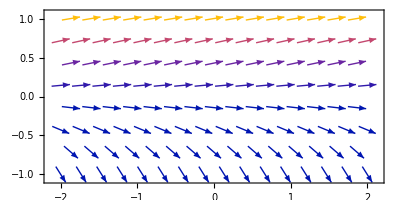

```mathematica
VectorPlot[{ⅇ^(-1/2 y^2) +ⅇ^(-9/2-y^2/2) √(π/2) Erfi[(3+y)/(√2)],y},{x,-2,2},{y,-1,1},AspectRatio->Automatic]
```

#### Bernoulli Equations

```mathematica
TraditionalForm[y'[x]+P[x]y[x]==Q[x]y[x]^n]
```

P(x) y(x)+y'(x)==Q(x) (y(x))^n

```mathematica
DSolve[y'[x]+11x y[x]==x^3 y[x]^3,y,x]
```

{{y→Function[{x},-11/(√(1+11 x^2+121 ⅇ^(11 x^2) C[1]))]},{y→Function[{x},11/(√(1+11 x^2+121 ⅇ^(11 x^2) C[1]))]}}

```mathematica
Column[Table[DSolve[y'[x]+P[x]y[x]==Q[x] y[x]^n,y[x],x],{n,1,5}]]
```

{{y[x]→ⅇ^((-P[K[1]]+Q[K[1]])K[1]1x) C[1]}}
{{y[x]→ⅇ^(-P[K[1]]K[1]1x)/(C[1]-ⅇ^(-P[K[1]]K[1]1K[2]) Q[K[2]]K[2]1x)}}
{{y[x]→-ⅇ^(-P[K[1]]K[1]1x)/(√(C[1]-2 ⅇ^(2 -P[K[1]]K[1]1K[2]) Q[K[2]]K[2]1x))},{y[x]→ⅇ^(-P[K[1]]K[1]1x)/(√(C[1]-2 ⅇ^(2 -P[K[1]]K[1]1K[2]) Q[K[2]]K[2]1x))}}
{{y[x]→ⅇ^(-P[K[1]]K[1]1x)/((C[1]-3 ⅇ^(3 -P[K[1]]K[1]1K[2]) Q[K[2]]K[2]1x)^(1/3))},{y[x]→-((-1)^(1/3) ⅇ^(-P[K[1]]K[1]1x))/((C[1]-3 ⅇ^(3 -P[K[1]]K[1]1K[2]) Q[K[2]]K[2]1x)^(1/3))},{y[x]→((-1)^(2/3) ⅇ^(-P[K[1]]K[1]1x))/((C[1]-3 ⅇ^(3 -P[K[1]]K[1]1K[2]) Q[K[2]]K[2]1x)^(1/3))}}
{{y[x]→-ⅇ^(-P[K[1]]K[1]1x)/((C[1]-4 ⅇ^(4 -P[K[1]]K[1]1K[2]) Q[K[2]]K[2]1x)^(1/4))},{y[x]→-(ⅈ ⅇ^(-P[K[1]]K[1]1x))/((C[1]-4 ⅇ^(4 -P[K[1]]K[1]1K[2]) Q[K[2]]K[2]1x)^(1/4))},{y[x]→(ⅈ ⅇ^(-P[K[1]]K[1]1x))/((C[1]-4 ⅇ^(4 -P[K[1]]K[1]1K[2]) Q[K[2]]K[2]1x)^(1/4))},{y[x]→ⅇ^(-P[K[1]]K[1]1x)/((C[1]-4 ⅇ^(4 -P[K[1]]K[1]1K[2]) Q[K[2]]K[2]1x)^(1/4))}}

Note that in general the solution to the Bernoulli equation has n-1 branches.

#### Riccati Equations

```mathematica
TraditionalForm[y'[x]==f[x]+g[x]y[x]+h[x]y[x]^2]
```

y'(x)==f(x)+g(x) y(x)+h(x) (y(x))^2

Where f≠0, h≠0.For if f is zero we get a Bernoulli Equation and if h is zero we get a linear ODE.

Here is an Example.

```mathematica
DSolve[y'[x]+2/x^2-3 y[x]^2==0,y[x],x]
```

{{y[x]→(-1+5 (-1+(2 C[1])/(x^5+C[1])))/(6 x)}}

```mathematica
Simplify[DSolve[y'[x]+2/x^2-3 y[x]^2==0,y[x],x]]
```

{{y[x]→-(3 x^5-2 C[1])/(3 x^6+3 x C[1])}}

Every non-linear Riccati equation can be reduced to a second order linear ODE via the change of variable  to get 
 
and then via the substitution 
 we get
.
With solution given by

For Example

```mathematica
DSolve[y'[x]==2 x/(1-x^2)y[x]-15/(4(1-x^2))-y[x]^2,y[x],x]//Simplify
```

{{y[x]→(5 (-x C[1] LegendreP[3/2,x]+C[1] LegendreP[5/2,x]-x LegendreQ[3/2,x]+LegendreQ[5/2,x]))/(2 (-1+x^2) (C[1] LegendreP[3/2,x]+LegendreQ[3/2,x]))}}

```mathematica
DSolve[(1-x^2)u''[x]-2x u'[x]+15/4 u[x]==0,u[x],x]
```

{{u[x]→C[1] LegendreP[3/2,x]+C[2] LegendreQ[3/2,x]}}

#### Exact Equations

```mathematica
P[x_,y_]:=-(5 x^2-2 y^2+11);
Q[x_,y_]:=Sin[y]+4 x y +3;
D[P[x,y],y]==D[Q[x,y],x]
```

True

```mathematica
DSolve[y'[x]==(-P[x,y[x]])/Q[x,y[x]],y[x],x]
```

Solve[-11 x-(5 x^3)/3-Cos[y[x]]+3 y[x]+2 x y[x]^2==C[1],y[x]]

We get a difficult equation to solve, but we can check that its solution is indeed a solution to the original ODE (by differentiating and solving for y’)

```mathematica
Solve[D[-11 x-(5 x^3)/3-Cos[y[x]]+3 y[x]+2 x y[x]^2==C[1],x],y'[x]]
```

{{y'[x]→(11+5 x^2-2 y[x]^2)/(3+Sin[y[x]]+4 x y[x])}}

We can use these types of solutions for example for a countourPlot of the solution

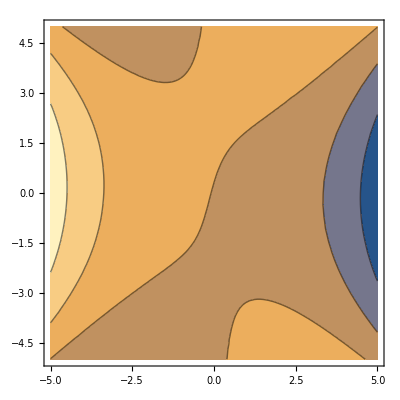

```mathematica
ContourPlot[-11 x-(5 x^3)/3-Cos[y[x]]+3 y[x]+2 x y[x]^2/.{y[x]->y},{x,-5,5},{y,-5,5}]
```

#### Clairaut Equations

```mathematica
TraditionalForm[y[x]==x y'[x]+f[y'[x]]]
```

y(x)==f(y'(x))+x y'(x)

```mathematica
DSolve[y[x]==x y[x]+f[y'[x]],y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[y[x]==f[y'[x]]+x y[x],y[x],x]

```mathematica
DSolve[x+Sin[y'[x]]==0,y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→-√(1-x^2)-x ArcSin[x]+C[1]}}

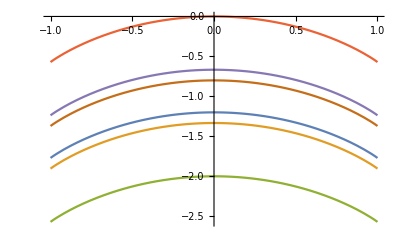

```mathematica
Plot[Evaluate[Table[y[x]/.{{y[x]->-√(1-x^2)-x ArcSin[x]+C[1]}}/.{C[1]->1/k},{k,-5,5,2}]],{x,-1,1}]
```

```mathematica
DSolve[y[x]==x y'[x] -Cos[y'[x]],y[x],x]
```

{{y[x]→x C[1]-Cos[C[1]]}}

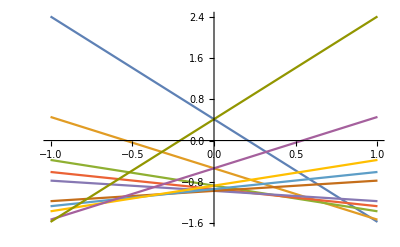

```mathematica
Plot[Evaluate[Table[y[x]/.%/.C[1]->k,{k,{-2,-1,-1/2,-1/3,-1/5,1/5,1/3,1/2,1,2}}]],{x,-1,1}]
```

```mathematica
y'[x]==y[x] +x y'[x] +Sin[y'[x]]y''[x]
```

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

```mathematica
y[x]==x y'[x] -Cos[y'[x]]/.{{y[x]->x C[1]-Cos[C[1]]}}
```

{x C[1]-Cos[C[1]]==-Cos[y'[x]]+x y'[x]}

```mathematica
%/.y[x]->x C[1] - Cos[C[1]]
```

{x C[1]-Cos[C[1]]==-Cos[y'[x]]+x y'[x]}

```mathematica
-√(1-x^2)-x ArcSin[x]+C[1]==x D[(-√(1-x^2)-x ArcSin[x]+C[1]),x]-Cos[D[-√(1-x^2)-x ArcSin[x]+C[1],x]]
```

-√(1-x^2)-x ArcSin[x]+C[1]==-√(1-x^2)-x ArcSin[x]

```mathematica
DSolve[y[x]==x y'[x]+1/2 y'[x]^2,y[x],x]
```

{{y[x]→x C[1]+C[1]^2/2}}

```mathematica
Eliminate[{x==-Sin[t],y==-Cos[t]-t Sin[t]},t]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

2 x y ArcSin[x]+x^2 ArcSin[x]^2==1-x^2-y^2

```mathematica
Reduce[2 x y ArcSin[x]+x^2 ArcSin[x]^2==1-x^2-y^2,y]
```

y==-√(1-x^2)-x ArcSin[x]||y==√(1-x^2)-x ArcSin[x]

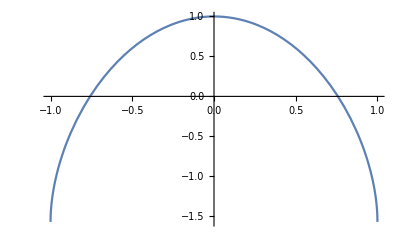

```mathematica
Plot[√(1-x^2)-x ArcSin[x],{x,-1,1}]
```

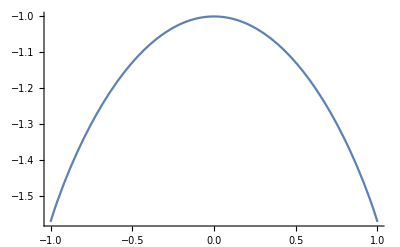

```mathematica
Plot[-√(1-x^2)-x ArcSin[x],{x,-1,1}]
```

#### Abel Equations

```mathematica
Clear[f,h,g,k]
```

```mathematica
invariant=f h^2+1/3(2 g^3/9-f g h -D[h, x] g + h D[g, x])
```

```mathematica
f0=0;f1=1/x;f2=-3;f3=x;
DSolve[y'[x]==f0+f1 y[x] +f2 y[x]^2+f3 y[x]^3,y,x]
```

{{y→Function[{x},1/x-1/(x^2 √(1/x^2+C[1]))]},{y→Function[{x},1/x+1/(x^2 √(1/x^2+C[1]))]}}